```mathematica
(*Defining the constant==============================*)
OmegM0 = 0.25; OmegR0 = 8*^-5; H0 = 2.3*^-18 (*1/s*); T0 = 2.7 (*K*);  (*OmegB0 = 0.04*) ;G = 6.67*^-8(*cm^3/g.s^2*);tstart = 340; tfin = 1000;(*s*)
OmegB0Arr = Array[.01 +#/100 &,10,0];
OmegB0 = OmegB0Arr[[4]];

Get["PlotLegends`"]

(*Defininng the useful relations=====================*)
a = Sqrt[2H0*t*Sqrt[OmegR0]]; 
T  = T0/(a*1*^9);
rhob0 = OmegB0*3*H0^2/(8*Pi*G);
rhob = rhob0/a^3;

(*Defining the Initial Conditons======================*)
initCond1 = XN[tstart]/XP[tstart]==1/7.3;
initCond2 = XD[tstart] == 0;
initCond3 = XN[tstart]+XP[tstart] == 1;
initCond4 = X3He[tstart] == 0;
initCond5 = X4He[tstart] == 0;
initCond6 = XT[tstart] == 0;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value {5.82897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

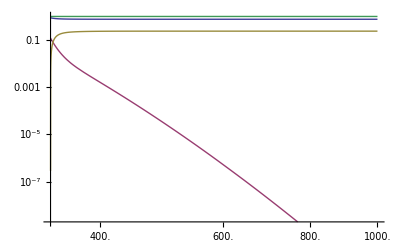

{1.}

```mathematica
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*Deterium, Protons and Neutrons Reaction 1========================*)
(*=====================================================*)
pn2d =2.5*^4*rhob;
d2pn = 4.68*^9*pn2d*T^(3/2)/rhob *Exp[-25.82/T];


eqN1 = XN'[t] == -XN[t]/882-XN[t]*XP[t]*pn2d+1/2*XD[t]*d2pn;
eqP1 = XP'[t] == XN[t]/882-XN[t]*XP[t]*pn2d+1/2*XD[t]*d2pn;
eqD1 = 1/2XD'[t] == XN[t]*XP[t]*pn2d-1/2*XD[t]*d2pn;

sol1 = NDSolve[{eqN1,eqP1,eqD1,initCond1, initCond2 ,initCond3 },{XN[t],XP[t],XD[t]},{t,tstart,tfin}];

XPSol1 = XP[t]/.sol1; XNSol1 = XN[t]/.sol1;XDSol1 = XD[t]/.sol1;  
Total1 =  XPSol1+XNSol1+XDSol1;

LogLogPlot[{XPSol1,XNSol1,XDSol1,Total1},{t,tstart,tfin},PlotLegend->{"XP","XN","XD","XP+XN+XD"}]
Total1/.t->tfin
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value {5.82897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

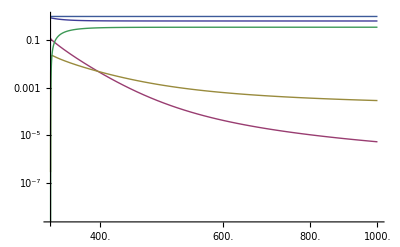

```mathematica
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*Now Adding He3========================================*)
(*=====================================================*)

(*From Reaction 2----------------------------*)
pd23he = 2.23*^3*rhob*T^(-2/3)Exp[-3.72*T^(-1/3)]*(1+0.112*T^(1/3) + 3.38*T^(2/3)+2.65*T);

he32pd = 1.63*^10*pd23he/rhob*T^(3/2)*Exp[-63.75/T];

eqN2 =c == 0;
eqP2 = XP'[t] == -1/2*XP[t]*XD[t]*pd23he +1/3*X3He[t]*he32pd;
eqD2 = 1/2*XD'[t] == -1/2*XP[t]*XD[t]*pd23he +1/3*X3He[t]*he32pd;
eq3He2 =1/3* X3He'[t] == 1/3*XN[t]*XD[t]*pd23he-1/3*X3He[t]*he32pd; 
(*---------------------------------------------*)

(*From Reaction 7------------------------------*)
(*Note that this reaction involves 2 Deuterium;
This there eill be a factor of 1/2 instead of 1/4
In front of XD[t]XD[t] and 2/3X3He[t]*)
dd2n3he = 3.9*^8*rhob*T^(-2/3)*Exp[-4.26*T^(-1/3)]*(1+0.0979*T^(1/3)+0.642*T^(2/3)+0.440*T);

n3he2dd = 1.73*dd2n3he*Exp[-37.94/T];

eqP7 = c ==0;
eqD7 =1/2XD'[t] ==   -1/2*XD[t]*XD[t]*dd2n3he+2/3*X3He[t]*XN[t]*n3he2dd;
eq3He7 = 1/3*X3He'[t] ==  1/4*XD[t]*XD[t]*dd2n3he-1/3*X3He[t]*XN[t]*n3he2dd;
eqN7 = XN'[t] ==  1/4*XD[t]*XD[t]*dd2n3he-1/3*X3He[t]*XN[t]*n3he2dd;
(*---------------------------------------------*)


(*Solving and Plotting-------------------------*)
sumXN =XN'[t]==(eqN1/.{Equal->List})[[2]] + (eqN2/.{Equal->List})[[2]]+(eqN7/.{Equal->List})[[2]];
sumXP = XP'[t] == (eqP1/.{Equal->List})[[2]]+ (eqP2/.{Equal->List})[[2]] + (eqP7/.{Equal->List})[[2]];
sumXD = 1/2*XD'[t]== (eqD1/.{Equal->List})[[2]]+ (eqD2/.{Equal->List})[[2]] + (eqD7/.{Equal->List})[[2]];
sumX3He = 1/3*X3He'[t] == (eq3He2/.{Equal->List})[[2]]+ (eq3He7/.{Equal->List})[[2]];



sol2 = NDSolve[{sumXN,sumXP, sumX3He,sumXD, initCond1, initCond2 ,initCond3,initCond4 },{XN[t],XP[t],XD[t],X3He[t]},{t,tstart,tfin}];

XPSol2 = XP[t]/.sol2; XNSol2 = XN[t]/.sol2;XDSol2 = XD[t]/.sol2; X3HeSol2 = X3He[t]/.sol2 ;
Total2 = XPSol2+XNSol2+XDSol2+X3HeSol2;
Total2/.t->tfin;

LogLogPlot[{XPSol2,XNSol2,XDSol2,X3HeSol2, Total2},{t,tstart,tfin},PlotLegend->{"XP","XN","XD","XHe3","XP+XN+XD+XHe3"}]
(*--------------------------------------------------------------*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value {5.82897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

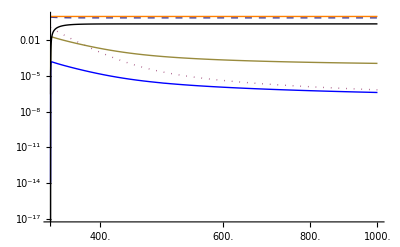

```mathematica
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*Now Adding He4========================================*)
(*=====================================================*)

(*Reaction 6-------------------------------------*)
n3He24He = 6*^3*rhob*T;
He42n3He = 2.6*^10*n3He24He/rhob*T^(3/2)*Exp[-238.8/T];

eqP6 =c==0;
eqD6 =c==0;
eqN6 = XN'[t] == -1/3*XN[t]*X3He[t]*n3He24He+1/4X4He[t]*He42n3He;
eq3He6 = 1/3*X3He'[t] == -1/3*XN[t]*X3He[t]*n3He24He+1/4X4He[t]*He42n3He;
eq4He6 = 1/4*X4He'[t] == +1/3*XN[t]*X3He[t]*n3He24He-1/4X4He[t]*He42n3He;
(*-----------------------------------------------*)
(*Reaction 9-------------------------------------*)
dd24he = 24.1*rhob*T^(-2/3)*Exp[-4.26*T^(-1/3)]*(T^(2/3)+0.685*T+0.152*T^(4/3)+0.265*T^(5/3));
he42dd = 4.5*^10*dd24he/rhob*T^(3/2)*Exp[-276.7/T];

eqP9 =c==0;
eqN9 =c==0;
eq3He9 =c==0;
eqD9 = 1/2*XD'[t] == -1/2XD[t]*XD[t]*dd24he + 1/2*X4He[t]*he42dd;
eq4He9 = 1/4*X4He'[t] == 1/4XD[t]*XD[t]*dd24he - 1/4*X4He[t]*he42dd;
(*------------------------------------------------*)

(*Reaction 10-------------------------------------*)
d3he2p4he = 2.60*^9*rhob*T^(-3/2)*Exp[-.745/T];
p4he2d3he = 5.5*d3he2p4he*Exp[-213/T];

eqN10 = c == 0;
eqD10 = 1/2*XD'[t] == -1/6*XD[t]*X3He[t]*d3he2p4he +1/4*XP[t]*X4He[t]*p4he2d3he;
eq3He10 = 1/3*X3He'[t] == -1/6*XD[t]*X3He[t]*d3he2p4he +1/4*XP[t]*X4He[t]*p4he2d3he;
eqP10 = XP'[t] == 1/6*XD[t]*X3He[t]*d3he2p4he -1/4*XP[t]*X4He[t]*p4he2d3he;
eq4He10 = 1/4*X4He'[t] == 1/6*XD[t]*X3He[t]*d3he2p4he -1/4*XP[t]*X4He[t]*p4he2d3he;

(*------------------------------------------------*)

(*Combining the equations-------------------------*)
sumXN2 =XN'[t]==(sumXN/.{Equal->List})[[2]] + (eqN6/.{Equal->List})[[2]]+(eqN9/.{Equal->List})[[2]]+(eqN10/.{Equal->List})[[2]];
sumXP2 =XP'[t]==(sumXP/.{Equal->List})[[2]] + (eqP6/.{Equal->List})[[2]]+(eqP9/.{Equal->List})[[2]]+(eqP10/.{Equal->List})[[2]];
sumXD2 =1/2*XD'[t]==(sumXD/.{Equal->List})[[2]] + (eqD6/.{Equal->List})[[2]]+(eqD9/.{Equal->List})[[2]]+(eqD10/.{Equal->List})[[2]];
sumX3He2 =1/3*X3He'[t]==(sumX3He/.{Equal->List})[[2]] + (eq3He6/.{Equal->List})[[2]]+(eq3He9/.{Equal->List})[[2]]+(eq3He10/.{Equal->List})[[2]];
sumX4He2 =1/4*X4He'[t]==(eq4He6/.{Equal->List})[[2]]+(eq4He9/.{Equal->List})[[2]]+(eq4He10/.{Equal->List})[[2]];


sol3 = NDSolve[{sumXN2,sumXP2, sumX3He2,sumXD2,sumX4He2, initCond1, initCond2 ,initCond3,initCond4,initCond5 },{XN[t],XP[t],XD[t],X3He[t],X4He},{t,tstart,tfin}];

XPSol3 = XP[t]/.sol3; XNSol3= XN[t]/.sol3;XDSol3 = XD[t]/.sol3; X3HeSol3 = X3He[t]/.sol3 ;X4HeSol3 = X4He[t]/.sol3 ;
Total3 =XPSol3+XNSol3+XDSol3+X3HeSol3+X4HeSol3; 
Total3/.t->tfin;

LogLogPlot[{XPSol3,XNSol3,XDSol3,X3HeSol3,X4HeSol3,  Total3},{t,tstart,tfin},PlotLegend->{"XP","XN","XD","XHe3","XHe4","XP+XN+XD+XHe3+XHe4"},PlotStyle->{Dashed,Dotted, Thick,Blue,Black,Orange}]

(*-------------------------------------------------*)
```

```mathematica
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*=====================================================*)
(*Now Adding T========================================*)
(*=====================================================*)


(*Reaction 3---------------------------------*)
nd2t = rhob*(75.5+1250*T);
t2nd = 1.63*^10*nd2t/rhob*T^(3/2)*Exp[-72.62/T];

eqP3 = c==0;
eq3He3 = c==0;
eq4He3 = c==0;
eqN3 = XN'[t] == -1/2*XN[t]*XD[t]*nd2t+1/3*XT[t]*t2nd;
eqD3 = 1/2*XD'[t] == -1/2*XN[t]*XD[t]*nd2t+1/3*XT[t]*t2nd;
eqT3 = 1/3*XT'[t] == 1/2*XN[t]*XD[t]*nd2t-1/3*XT[t]*t2nd;

(*--------------------------------------------*)

(*Reaction 4---------------------------------*)
n3he2pt = 7.06*^8*rhob;
pt2n3he = n3he2pt*Exp[-8.864/T];

eqD4 = c==0;
eq4He4 = c==0;
eqN4 = XN'[t] == -1/3*XN[t]*X3He[t]*n3he2pt+1/3*XP[t]*XT[t]*pt2n3he;
eq3He4 = 1/3*X3He'[t] == -1/3*XN[t]*X3He[t]*n3he2pt+1/3*XP[t]*XT[t]*pt2n3he;
eqP4 = XP'[t] == 1/3*XN[t]*X3He[t]*n3he2pt-1/3*XP[t]*XT[t]*pt2n3he;
eqT4 = 1/3*XT'[t] == 1/3*XN[t]*X3He[t]*n3he2pt-1/3*XP[t]*XT[t]*pt2n3he;
(*--------------------------------------------*)

(*Reaction 5---------------------------------*)
pt24he = 2.87*^4*rhob*T^(-2/3)*Exp[-3.87*T^(-1/3)]*(1+0.108*T^(1/3)+0.466*T^(2/3)+0.352*T+0.300*T^(4/3)+0.576*T^(5/3));
he42pt = 2.59*^10*pt24he/rhob*T^(3/2)*Exp[-229.9/T];

eqD5 = c==0;
eq3He5 = c==0;
eqN5= c == 0;
eqP5 = XP'[t] == -1/3*XP[t]*XT[t]*pt24he +1/4*X4He[t]*he42pt;
eqT5 =1/3* XT'[t] == -1/3*XP[t]*XT[t]*pt24he +1/4*X4He[t]*he42pt;
eq4He5 =1/4* X4He'[t] == 1/3*XP[t]*XT[t]*pt24he -1/4*X4He[t]*he42pt;

(*--------------------------------------------*)
(*Reaction 8---------------------------------*)
dd2pt = dd2n3he;
pt2dd = 1.73*dd2pt*Exp[-46.80/T];

eqN8 = c == 0;
eq3He8 = c == 0;
eq4He8 = c == 0;
eqD8 = 1/2*XD'[t]==-1/2*XD[t]*XD[t]*dd2pt+(2/3)*XP[t]*XT[t]*pt2dd;
eqP8 = XP'[t]==1/4*XD[t]*XD[t]*dd2pt-1/3*XP[t]*XT[t]*pt2dd;eqT8 = 1/3*XT'[t]==1/4*XD[t]*XD[t]*dd2pt-1/3*XP[t]*XT[t]*pt2dd;
(*--------------------------------------------*)


(*Reaction 11---------------------------------*)
dt2n4he = 1.38*^9*rhob*T^(-3/2)*Exp[-0.745/T];
n4he2dt = 5.5*dt2n4he*Exp[-204.1/T];

eqP11 = c == 0;
eq3He11 = c ==0;
eqD11 = 1/2*XD'[t] == -1/6*XD[t]*XT[t]*dt2n4he+1/4*X4He[t]XN[t]*n4he2dt;
eqT11 = 1/3*XT'[t] == -1/6*XD[t]*XT[t]*dt2n4he+1/4*X4He[t]XN[t]*n4he2dt;
eq4He11 = 1/4*X4He'[t] == 1/6*XD[t]*XT[t]*dt2n4he-1/4*X4He[t]XN[t]*n4he2dt;
eqN11 = XN'[t] == 1/6*XD[t]*XT[t]*dt2n4he-1/4*X4He[t]XN[t]*n4he2dt;
(*--------------------------------------------*)

(*Reaction 15---------------------------------*)
t3he2d4he = 3.88*^9*rhob*T^(-2/3)*Exp[-7.72*T^(-1/3)]*(1+0.0540*T^(1/3));
d4he2t3he = 1.59*t3he2d4he*Exp[-166.2/T];

eqN15 = c == 0;
eqP15 = c == 0;
eq3He15 = 1/3*X3He'[t] ==-1/9*X3He[t]*XT[t]*t3he2d4he + 1/8*X4He[t]*XD[t]*d4he2t3he;
eqT15 = 1/3*XT'[t] ==-1/9*X3He[t]*XT[t]*t3he2d4he + 1/8*X4He[t]*XD[t]*d4he2t3he;
eq4He15 = 1/4*X4He'[t] ==1/9*X3He[t]*XT[t]*t3he2d4he - 1/8*X4He[t]*XD[t]*d4he2t3he;
eqD15 = 1/2*XD'[t] ==1/9*X3He[t]*XT[t]*t3he2d4he - 1/8*X4He[t]*XD[t]*d4he2t3he;
(*--------------------------------------------*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value {5.82897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

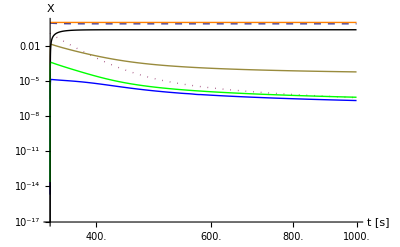

```mathematica
(*Combining the equations-------------------------*)
sumXN3 =XN'[t]==(sumXN2/.{Equal->List})[[2]] + (eqN3/.{Equal->List})[[2]]+(eqN4/.{Equal->List})[[2]]+(eqN5/.{Equal->List})[[2]]+ (eqN8/.{Equal->List})[[2]]+(eqN11/.{Equal->List})[[2]]+(eqN15/.{Equal->List})[[2]];
sumXP3 =XP'[t]==(sumXP2/.{Equal->List})[[2]] + (eqP3/.{Equal->List})[[2]]+(eqP4/.{Equal->List})[[2]]+(eqP5/.{Equal->List})[[2]]+ (eqP8/.{Equal->List})[[2]]+(eqP11/.{Equal->List})[[2]]+(eqP15/.{Equal->List})[[2]];
sumXD3 =1/2*XD'[t]==(sumXD2/.{Equal->List})[[2]] + (eqD3/.{Equal->List})[[2]]+(eqD4/.{Equal->List})[[2]]+(eqD5/.{Equal->List})[[2]]+(eqD8/.{Equal->List})[[2]]+(eqD11/.{Equal->List})[[2]]+(eqD15/.{Equal->List})[[2]];
sumX3He3 =1/3*X3He'[t]==(sumX3He2/.{Equal->List})[[2]] + (eq3He3/.{Equal->List})[[2]]+(eq3He4/.{Equal->List})[[2]]+(eq3He5/.{Equal->List})[[2]]+ (eq3He8/.{Equal->List})[[2]]+(eq3He11/.{Equal->List})[[2]]+(eq3He15/.{Equal->List})[[2]];
sumX4He3 =1/4*X4He'[t]==(sumX4He2/.{Equal->List})[[2]] +(eq4He3/.{Equal->List})[[2]]+(eq4He4/.{Equal->List})[[2]]+(eq4He5/.{Equal->List})[[2]]+(eq4He8/.{Equal->List})[[2]]+(eq4He11/.{Equal->List})[[2]]+(eq4He15/.{Equal->List})[[2]];
sumXT3 =1/3*XT'[t]==(eqT3/.{Equal->List})[[2]]+(eqT4/.{Equal->List})[[2]]+(eqT5/.{Equal->List})[[2]]+(eqT8/.{Equal->List})[[2]]+(eqT11/.{Equal->List})[[2]]+(eqT15/.{Equal->List})[[2]];





sol4 = NDSolve[{sumXN3,sumXP3, sumX3He3,sumXD3, sumX4He3,sumXT3, initCond1, initCond2 ,initCond3,initCond4,initCond5,initCond6 },{XN[t],XP[t],XD[t],X3He[t],X4He[t],XT[t]},{t,tstart,tfin}];

XPSol4 = XP[t]/.sol4; XNSol4= XN[t]/.sol4;XDSol4 = XD[t]/.sol4; X3HeSol4 = X3He[t]/.sol4 ;X4HeSol4 = X4He[t]/.sol4 ;XTSol4 = XT[t]/.sol4;
Total4 = XPSol4+XNSol4+XDSol4+X3HeSol4+X4HeSol4+XTSol4;
LogLogPlot[{XPSol4,XNSol4,XDSol4,X3HeSol4,X4HeSol4,  XTSol4,Total4},{t,tstart,tfin},PlotLegend->{"XP","XN","XD","XHe3","XHe4","XT","Total"},PlotStyle->{{Dashed,Thick},{Dotted,Thick}, Thick,Blue,Black,Green,Orange},AxesLabel->{"t [s]","X"}]


(*-------------------------------------------------*)
```